```mathematica
$Assumptions={X>0,n>0,a>0,d>0,q>0,t>0,z>0,w>0,α>0,β>0,σ>0,s>0,h>0,m>0,,z∈ Reals,px2∈ Reals,py2∈ Reals,px1∈ Reals,py1∈ Reals,px∈ Reals,py∈ Reals,r∈ Reals,r1∈ Reals,r2∈ Reals,x1∈ Reals,x2∈ Reals,x∈ Reals,w∈ Reals,t∈ Reals,k1∈ Reals,k2∈ Reals,k∈ Reals,n∈ Reals,q∈ Reals,a∈ Reals,d∈ Reals,p∈ Reals,p1∈ Reals,p2∈ Reals,y1∈Reals,y2∈Reals,α∈Reals,β∈Reals,σ∈Reals,s∈Reals,v1∈Reals,v2∈Reals,β1∈Reals,β2∈Reals,X∈Reals,h∈Reals,m∈
Reals}
```

{X>0,n>0,a>0,d>0,q>0,t>0,z>0,w>0,α>0,β>0,σ>0,s>0,h>0,m>0,Null,z∈Reals,px2∈Reals,py2∈Reals,px1∈Reals,py1∈Reals,px∈Reals,py∈Reals,r∈Reals,r1∈Reals,r2∈Reals,x1∈Reals,x2∈Reals,x∈Reals,w∈Reals,t∈Reals,k1∈Reals,k2∈Reals,k∈Reals,n∈Reals,q∈Reals,a∈Reals,d∈Reals,p∈Reals,p1∈Reals,p2∈Reals,y1∈Reals,y2∈Reals,α∈Reals,β∈Reals,σ∈Reals,s∈Reals,v1∈Reals,v2∈Reals,β1∈Reals,β2∈Reals,X∈Reals,h∈Reals,m∈Reals}

```mathematica
(ⅇ^(-(d-x)^2/(4 σ^2))ⅇ^(ⅈ p0 x))/(√(2 π) σ)^(1/2)
```

(ⅇ^(ⅈ p0 x-(d-x)^2/(4 σ^2)))/((2 π)^(1/4) √σ)

```mathematica
Integrate[(ⅇ^(ⅈ p0 x-(d-x)^2/(4 σ^2)))/((2 π)^(1/4) √σ)(ⅇ^(-ⅈ p0 x-(d-x)^2/(4 σ^2)))/((2 π)^(1/4) √σ),{x,-∞,∞}]
```

1

```mathematica
(ⅇ^(-(d-x)^2/(4 σ^2))ⅇ^(ⅈ p0 x)+ⅇ^(-(d+x)^2/(4 σ^2))ⅇ^(-ⅈ p0 x))/((2 (1+ⅇ^(-(d^2+4 p0^2 σ^4)/(2 σ^2))) √(2 π) σ)^(1/2))
```

(ⅇ^(ⅈ p0 x-(d-x)^2/(4 σ^2))+ⅇ^(-ⅈ p0 x-(d+x)^2/(4 σ^2)))/(2^(3/4) π^(1/4) √((1+ⅇ^(-(d^2+4 p0^2 σ^4)/(2 σ^2))) σ))

```mathematica
(ⅇ^(-(d-x)^2/(2 σ^2))+ⅇ^(-(d+x)^2/(2 σ^2))+ⅇ^(-(d-x)^2/(4 σ^2)-(d+x)^2/(4 σ^2)) (2 Cos[2 p0 x]))/(2 (1+ⅇ^(-(d^2+4 p0^2 σ^4)/(2 σ^2))) √(2 π) σ)
```

(ⅇ^(-(d-x)^2/(2 σ^2))+ⅇ^(-(d+x)^2/(2 σ^2))+2 ⅇ^(-(d-x)^2/(4 σ^2)-(d+x)^2/(4 σ^2)) Cos[2 p0 x])/(2 (1+ⅇ^(-(d^2+4 p0^2 σ^4)/(2 σ^2))) √(2 π) σ)

```mathematica
Integrate[(ⅇ^(-(d-x)^2/(2 σ^2))+ⅇ^(-(d+x)^2/(2 σ^2))+2 ⅇ^(-(d-x)^2/(4 σ^2)-(d+x)^2/(4 σ^2)) Cos[2 p0 x])/(2 (1+ⅇ^(-(d^2+4 p0^2 σ^4)/(2 σ^2))) √(2 π) σ),{x,-∞,∞}]
```

1

```mathematica
Integrate[(ⅇ^(ⅈ p0 x-(d-x)^2/(4 σ^2))+ⅇ^(-ⅈ p0 x-(d+x)^2/(4 σ^2)))/(2^(3/4) π^(1/4) √((1+ⅇ^(-(d^2+4 p0^2 σ^4)/(2 σ^2))) σ))(ⅇ^(-ⅈ p0 x-(d-x)^2/(4 σ^2))+ⅇ^(ⅈ p0 x-(d+x)^2/(4 σ^2)))/(2^(3/4) π^(1/4) √((1+ⅇ^(-(d^2+4 p0^2 σ^4)/(2 σ^2))) σ)),{x,-∞,∞}]
```

1

```mathematica
(ⅇ^(-(x-d+t)^2/(2 σ^2))+ⅇ^(-(x+d-t)^2/(2 σ^2))+2 ⅇ^(-(x-d+t)^2/(4 σ^2)-(x+d-t)^2/(4 σ^2)) Cos[2 p0 x-t])/(2 (1+ⅇ^(-(d^2+4 p0^2 σ^4)/(2 σ^2))) √(2 π) σ)
```

(ⅇ^(-(d-t+x)^2/(2 σ^2))+ⅇ^(-(-d+t+x)^2/(2 σ^2))+2 ⅇ^(-(d-t+x)^2/(4 σ^2)-(-d+t+x)^2/(4 σ^2)) Cos[t-2 p0 x])/(2 (1+ⅇ^(-(d^2+4 p0^2 σ^4)/(2 σ^2))) √(2 π) σ)

```mathematica
collids[p0_, d_, σ_, x_,t_]:= ⅇ^(-(d-t+x)^2/(2 σ^2))+ⅇ^(-(-d+t+x)^2/(2 σ^2))
```

```mathematica
Animate[Plot[collids[1,5,1,x,t],{x,-10,10}],{t,0,10}]
```

```mathematica
Integrate[(ⅇ^(ⅈ p0 x-(d-x)^2/(4 σ^2))+ⅇ^(-ⅈ p0 x-(d+x)^2/(4 σ^2)))ⅇ^(ⅈ p x),{x,-∞,∞}]
```

2 (ⅇ^(-(p-p0) (ⅈ d+(p-p0) σ^2))+ⅇ^(-(p+p0) (-ⅈ d+(p+p0) σ^2))) √π σ

```mathematica
ⅇ^(- (ⅈ d (p-p0)+(p-p0)(p-p0) σ^2))+ⅇ^(- (-ⅈ d (p+p0)+(p+p0)(p+p0) σ^2))
```

ⅇ^(-ⅈ d (p-p0)-(p-p0)^2 σ^2)+ⅇ^(ⅈ d (p+p0)-(p+p0)^2 σ^2)

```mathematica
(ⅇ^(ⅈ (-a p^2 t+p x))ⅇ^(-ⅈ d (p-p0)-(p-p0)^2 σ^2)+ⅇ^(ⅈ (-a p^2 t+p x))ⅇ^(ⅈ d (p+p0)-(p+p0)^2 σ^2))
```

```mathematica
q = p-p0
```

```mathematica
Integrate[ⅇ^(ⅈ (- a q^2 t-q (2 a p0 t+x)))ⅇ^(-ⅈ d q-q^2 σ^2),{q,-∞,∞}]
```

(ⅇ^((ⅈ (d+2 a p0 t+x)^2)/(4 a t-4 ⅈ σ^2)) √π)/(√(ⅈ a t+σ^2))

```mathematica
Integrate[ⅇ^(ⅈ x p0)ⅇ^(-ⅈ a p0^2)ⅇ^(ⅈ (- a q^2 t-q (2 a p0 t+x)))ⅇ^(-ⅈ d q-q^2 σ^2),{q,-∞,∞}]
```

(ⅇ^((ⅈ (d^2+4 a^2 p0^2 (-1+t) t+2 d (2 a p0 t+x)+4 a p0 (2 t x+ⅈ p0 σ^2)+x (x-4 ⅈ p0 σ^2)))/(4 a t-4 ⅈ σ^2)) √π)/(√(ⅈ a t+σ^2))

```mathematica
Integrate[ⅇ^(ⅈ (-a p^2 t+p x))ⅇ^(-ⅈ d (p-p0)-(p-p0)^2 σ^2),{p,-∞,∞}]
```

```mathematica
FullSimplify[ⅇ^((ⅈ (d^2-2 d x+x^2+4 ⅈ a p0^2 t σ^2+4 ⅈ p0 x σ^2))/(4 a t-4 ⅈ σ^2)) (ⅇ^((ⅈ d (a p0 t+x))/(a t-ⅈ σ^2))+ⅇ^((p0 (ⅈ a d t+2 x σ^2))/(a t-ⅈ σ^2)))]
```

ⅇ^((ⅈ (d^2+x^2+2 d (2 a p0 t+x))-4 p0 (a p0 t+x) σ^2)/(4 a t-4 ⅈ σ^2)) (1+ⅇ^((x (d+2 ⅈ p0 σ^2))/(ⅈ a t+σ^2)))

```mathematica
Simplify[(ⅇ^((ⅈ (d^2+x^2+2 d (2 a p0 t+x))-4 p0 (a p0 t+x) σ^2)/(4 a t-4 ⅈ σ^2)) (1+ⅇ^((x (d+2 ⅈ p0 σ^2))/(ⅈ a t+σ^2))))(ⅇ^((-ⅈ (d^2+x^2+2 d (2 a p0 t+x))-4 p0 (a p0 t+x) σ^2)/(4 a t+4 ⅈ σ^2)) (1+ⅇ^((x (d-2 ⅈ p0 σ^2))/(-ⅈ a t+σ^2))))]
```

ⅇ^(-((d+2 a p0 t+x)^2 σ^2)/(2 (a^2 t^2+σ^4))) (1+ⅇ^((x (d-2 ⅈ p0 σ^2))/(-ⅈ a t+σ^2))) (1+ⅇ^((x (d+2 ⅈ p0 σ^2))/(ⅈ a t+σ^2)))

```mathematica
(1+ⅇ^((x (d-2 ⅈ p0 σ^2))/(-ⅈ a t+σ^2)) + ⅇ^((x (d+2 ⅈ p0 σ^2))/(ⅈ a t+σ^2))+ⅇ^((x (d+2 ⅈ p0 σ^2))/(ⅈ a t+σ^2))ⅇ^((x (d-2 ⅈ p0 σ^2))/(-ⅈ a t+σ^2)))
```

```mathematica
1+ⅇ^((x (d-2 ⅈ p0 σ^2))/(-ⅈ a t+σ^2))+ⅇ^((x (d+2 ⅈ p0 σ^2))/(ⅈ a t+σ^2))+ⅇ^((2 (d+2 a p0 t) x σ^2)/(a^2 t^2+σ^4))
```

1+ⅇ^((x (d-2 ⅈ p0 σ^2))/(-ⅈ a t+σ^2))+ⅇ^((x (d+2 ⅈ p0 σ^2))/(ⅈ a t+σ^2))+ⅇ^((2 (d+2 a p0 t) x σ^2)/(a^2 t^2+σ^4))

```mathematica
(ⅇ^(-((d+2 a p0 t+x)^2 σ^2)/(2 (a^2 t^2+σ^4)))+ⅇ^(-((d+2 a p0 t+x)^2 σ^2)/(2 (a^2 t^2+σ^4)))ⅇ^((x (d-2 ⅈ p0 σ^2))/(-ⅈ a t+σ^2))+ⅇ^(-((d+2 a p0 t+x)^2 σ^2)/(2 (a^2 t^2+σ^4)))ⅇ^((x (d+2 ⅈ p0 σ^2))/(ⅈ a t+σ^2))+ⅇ^(-((d+2 a p0 t+x)^2 σ^2)/(2 (a^2 t^2+σ^4)))ⅇ^((2 (d+2 a p0 t) x σ^2)/(a^2 t^2+σ^4)))
```

```mathematica
ⅇ^(-((d+2 a p0 t+x)^2 σ^2)/(2 (a^2 t^2+σ^4)))(1+ⅇ^((x (d-2 ⅈ p0 σ^2))/(-ⅈ a t+σ^2))+ⅇ^((x (d+2 ⅈ p0 σ^2))/(ⅈ a t+σ^2)))+ⅇ^(-((d+2 a p0 t-x)^2 σ^2)/(2 (a^2 t^2+σ^4)))
```

ⅇ^(-((d+2 a p0 t-x)^2 σ^2)/(2 (a^2 t^2+σ^4)))+ⅇ^(-((d+2 a p0 t+x)^2 σ^2)/(2 (a^2 t^2+σ^4))) (1+ⅇ^((x (d-2 ⅈ p0 σ^2))/(-ⅈ a t+σ^2))+ⅇ^((x (d+2 ⅈ p0 σ^2))/(ⅈ a t+σ^2)))

```mathematica
ExpToTrig[1+ⅇ^((x (d-2 ⅈ p0 σ^2))/(-ⅈ a t+σ^2))+ⅇ^((x (d+2 ⅈ p0 σ^2))/(ⅈ a t+σ^2))]
```

1+Cosh[(x (d-2 ⅈ p0 σ^2))/(-ⅈ a t+σ^2)]+Cosh[(x (d+2 ⅈ p0 σ^2))/(ⅈ a t+σ^2)]+Sinh[(x (d-2 ⅈ p0 σ^2))/(-ⅈ a t+σ^2)]+Sinh[(x (d+2 ⅈ p0 σ^2))/(ⅈ a t+σ^2)]

```mathematica
FileLists=0;
FileLists=ReadList["/Users/cricha5/Desktop/Physics/SchrodOrigins/ChrisFiniteDifferenceTransitionOMP/ChrisFiniteDifferenceTransitionOMP/probdata_collide_ep-0.dat",Number,RecordLists->True];
```

```mathematica
FileLists2=0;
FileLists2=ReadList["/Users/cricha5/Desktop/Physics/SchrodOrigins/ChrisFiniteDifferenceTransitionOMP/ChrisFiniteDifferenceTransitionOMP/probdata_collide_ep-5.dat",Number,RecordLists->True];
```

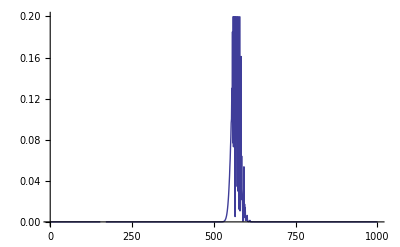

```mathematica
ListLinePlot[FileLists,PlotRange->{Full,{0,0.2}}]
```

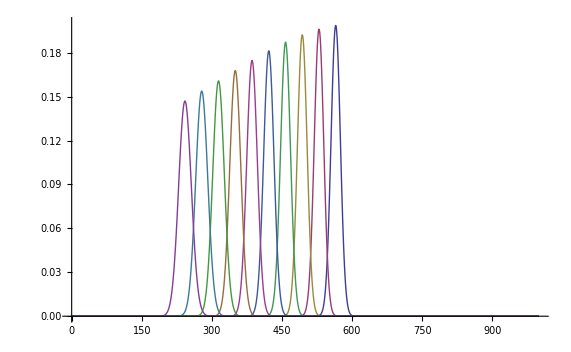

```mathematica
ListLinePlot[FileLists2,PlotRange->{Full,{0,0.2}}]
```

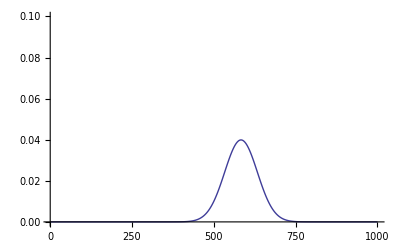

```mathematica
ListLinePlot[FileLists⟦1, All⟧, PlotRange->{Full,{0,0.1}}]
```